#### Initial Work on Newton relaxation. I am thinking that NMinimize with constraints may be a better method to find a better solution

```mathematica
findNotNearestNeighborUpToDistance[positions_,nf_,whichParticle_,beyondNearstNeighbor_, distance_]:=
Select[Abs[#Index-whichParticle] >1 &][nf[positions[[whichParticle]],{beyondNearstNeighbor + 3,distance}]]
```

```mathematica
checkCollisions[positions_,nf_,whichParticle_,beyondNearstNeighbor_,distance_]:= Block[{numberCollisions},
numberCollisions=Echo@Length[findNotNearestNeighborUpToDistance[positions,nf,whichParticle,beyondNearstNeighbor,distance]];
If[
numberCollisions > 0,Throw[numberCollisions]
];
numberCollisions
]
```

#### The following has not be checked. So far, only the newton relaxation has been check.

```mathematica
displacementsNew[perturbedIndex_,positionList_,s_,ν_,θ_,OptionsPattern[]]:= 
Block[{displacement,displacedPositions,betaList,Δ , computedPositions,collisionDistance,results,overlap,minDistances ,currentNearest,indexRules, selectCollisions},
Δ=precompute[positionList,perturbedIndex,s,ν,θ];
displacement[perturbedIndex] =positionList[[perturbedIndex]]+s AngleVector[θ];
computedPositions = {displacement[perturbedIndex]};
indexRules=<|1->perturbedIndex|>;
selectCollisions=Select[Abs[#Particle - #OtherParticle]> 1 && #Distance <1&];
(*#1*)
 displacement[index_] := displacement[index]=
Module[{nextIndex=index-Sign[index-perturbedIndex],myDisplacement},
myDisplacement=displacement[index-nextIndex ]+ Δ[[index]];
AppendTo[computedPositions,myDisplacement];
AssociateTo[indexRules,Length[computedPositions]->index];
myDisplacement
];

newPositions = displacement/@Range[Length[Δ]];
currentNearest =Nearest[newPositions->All];
If[
0== Catch[MapIndexed[checkCollisions[#1,currentNearest,#2[[1]],2,1]&,newPositions]],
Return[newPositions],
True,Return[newtonRelaxation[newPositions,currentNearest]]
]
]
```

Not sure if this is too singular, but it needs to go to zero at r=1

```mathematica
energy =With[{r = Sqrt[(xOther - xMe)^2 + (yOther - yMe)^2]},1/r^12]
```

1/(((-xMe+xOther)^2+(-yMe+yOther)^2)^6)

```mathematica
Grad[-energy,{xMe,yMe}]
```

{-(12 (-xMe+xOther))/(((-xMe+xOther)^2+(-yMe+yOther)^2)^7),-(12 (-yMe+yOther))/(((-xMe+xOther)^2+(-yMe+yOther)^2)^7)}

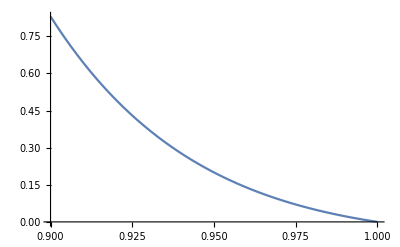

```mathematica
Plot[(1-x^2)/x^14,{x,.9,1}]
```

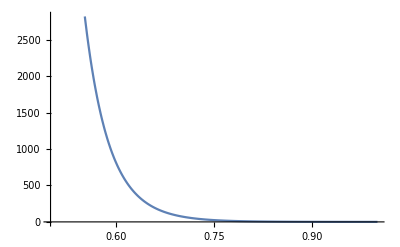

```mathematica
Plot[(1-x^2)/x^14,{x,0.5,1}]
```

```mathematica
force[pMe:{xMe_,yMe_},pOther:{xOther_,yOther_}]:= Block[{dp = pOther-pMe,magSq},
magSq= dp.dp;
(-dp (1-magSq))/(magSq)^4]
```

```mathematica
computeForceInNeighborhood[position_,neighborhood_List]:=
Block[{ positions},
If[Length[neighborhood]==0,Return[{0,0}]];
positions =neighborhood[[All,"Element"]];
Total[force[position,#]&/@positions]
]
```

```mathematica
newtonRelaxation[positions_,nf_]:= Block[{relaxedPositions = positions, forces,maxForceMagnitude,neighborhoods, currentNearest = nf,overlaps,selector =Select[#Distance < 1&],icount=0},
neighborhoods =Select[!PossibleZeroQ[#Distance]&][#]&/@currentNearest[relaxedPositions,{13,1}];
overlaps =Length[Flatten[selector/@neighborhoods]];
While[overlaps >0 && icount++ < 200,
forces =MapThread[computeForceInNeighborhood[#1,#2]&,{relaxedPositions,neighborhoods}];
maxForceMagnitude = Max[Norm/@forces];
If[maxForceMagnitude==0,Break[]];
forces = 0.01 forces/maxForceMagnitude; (*is 0.01 a good choice?*)
relaxedPositions += forces;
currentNearest=Nearest[relaxedPositions->All];
neighborhoods =Select[!PossibleZeroQ[#Distance]&][#]&/@currentNearest[relaxedPositions,{13,1}];
overlaps =Length[Flatten[Select[#Distance < 1&][#]&/@neighborhoods]];
];
{overlaps,relaxedPositions}
]
```

```mathematica
positions=AnglePath[ConstantArray[0.565,10]]
```

{{0.,0.},{0.844589,0.535416},{1.27125,1.43983},{1.14736,2.43212},{0.511441,3.20388},{-0.438861,3.51521},{-1.40817,3.26935},{-2.09519,2.54271},{-2.2864,1.56116},{-1.92235,0.629785},{-1.1162,0.038069}}

#### displacements is the non-collision detecting version in the beginning of Random_Motion_of_Polymer.nb

```mathematica
positions=displacements[11,positions,.126,.1,0]
```

{{-0.502952,0.0040433},{0.371188,0.489717},{0.885964,1.34704},{0.874841,2.34698},{0.311374,3.17312},{-0.626668,3.51964},{-1.58831,3.24533},{-2.2107,2.46263},{-2.29072,1.46583},{-1.83258,0.576948},{-0.990202,0.038069}}

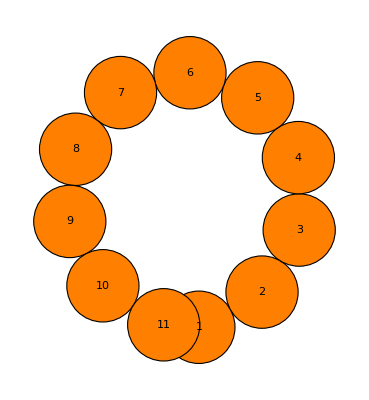

```mathematica
Graphics[chainGraphic[positions]]
```

```mathematica
Length[positions]
```

11

```mathematica
nf= Nearest[positions->All]
```

NearestFunction[…]

```mathematica
{overlaps,relaxedPositions}=newtonRelaxation[positions,nf]
```

{0,{{-0.244544,-0.177238},{0.480392,0.51215},{0.959119,1.39084},{0.899941,2.38963},{0.315799,3.20186},{-0.625326,3.54143},{-1.58988,3.27574},{-2.23359,2.50979},{-2.36414,1.51777},{-1.95471,0.60468},{-1.24183,-0.0972952}}}

```mathematica
Union[Flatten[DistanceMatrix[relaxedPositions]]]
```

{0.,1.00039,1.00047,1.00048,1.00048,1.00048,1.00051,1.00052,1.00054,1.00057,1.00063,1.00069,1.82687,1.88044,1.90711,1.9107,1.9113,1.92092,1.92189,1.92378,1.92541,1.96673,1.97678,2.43686,2.64165,2.6428,2.65682,2.66808,2.67124,2.69474,2.69586,2.71399,2.78935,2.81045,3.01706,3.01802,3.13583,3.16516,3.17021,3.22362,3.22477,3.28207,3.32568,3.34311,3.36676,3.3699,3.37852,3.38311,3.39095,3.42524,3.44971,3.45304,3.64837,3.69058,3.70581,3.73811}

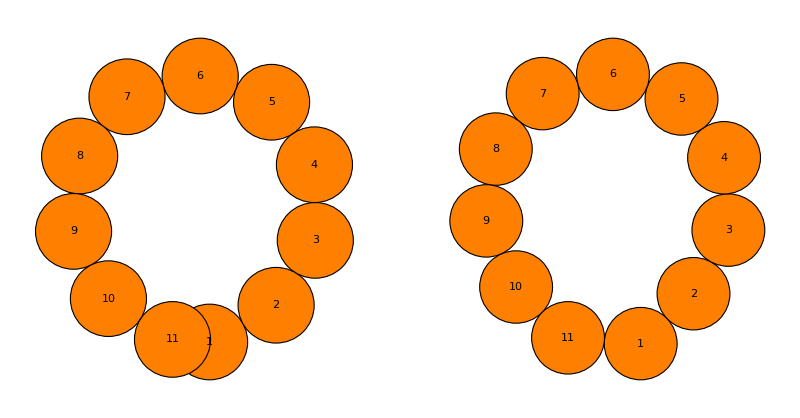

```mathematica
GraphicsRow[{Graphics[chainGraphic[positions]],Graphics[chainGraphic[relaxedPositions]]}]
```

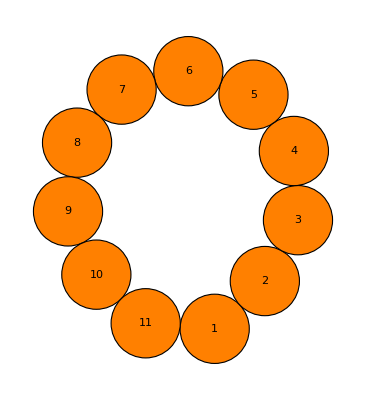

```mathematica
Graphics[chainGraphic[tmp]]
```

```mathematica
Plot[(1-x^2)/x^12,{x,0.5,1}]
```